# Volume Measurement

A region about a vertex c is a set X of vertices, and its volume is a count. The regions here are the ball, the shell, the tube about the interval of two vertices or about one geodesic, the solid ellipsoid of two foci, the cone about a geodesic and the sphere instance in a band. Each has a size parameter, and its profile is its volume as a function of the size.

Every region is measured twice. The counting measure is Abs[X]. The Riemannian measure is Abs[X|-|∂X|==|IntX], where the boundary ∂X is the set of vertices of X with a neighbour outside X, and the interior IntX is the rest.

The questions: which closed formula each profile follows on a lattice, which formula of the continuum it approaches, why either measure stands for the volume of a region of the limit space, and which dimension the profiles read.

Each 3 × 3 figure is one substrate at one size: the rows are the sizes small, medium and large, the columns the square tiling, the triangular tiling and an irregular mesh of the square. The pictures keep the embedding of the substrate; no measurement uses it.

## Setup

```mathematica
Needs["WolframInstitute`InfraGeometry`"]
```

The centre c is a vertex of least eccentricity. The profiles run up to R==⌊(ecc(c)-1)/2⌋, so that a tube of thickness R about a segment of length R from c stays inside the graph.

```mathematica
profileRadius[g_] := Floor[(VertexEccentricity[g, InfraCenter[g]] - 1)/2]
```

The far end p of the segments: a vertex at distance R from the centre, drawn after a seed.

```mathematica
farEnd[g_] := (SeedRandom[1]; RandomInfraPoint[g, InfraCenter[g], profileRadius[g]])
```

The two measures of a list of regions: the counting measure first, the Riemannian measure second.

```mathematica
twoMeasures[g_, regions_] := InfraMeasurement[g, regions, #] & /@ {"CountingMeasure", "RiemannianMeasure"}
```

A region drawn by its two measures: the interior green, the boundary blue. The counting measure counts both colours, the Riemannian measure the green vertices only.

```mathematica
interiorAndBoundary[g_, region_] := With[{support = FindInfraRepresentative[g, region]}, {InfraInterior[g, support] -> $InfraBallColor, InfraBoundary[g, support] -> $InfraCircleColor}]
```

## Balls

The ball is B_r(c)=={v:d(c,v)≤r}. Below, the ball of radius R about the centre.

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size, "KeepCoordinates" -> True])},
    InfraSubstrateHighlight[g, interiorAndBoundary[g, InfraBall[InfraCenter[g], profileRadius[g]]]]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

The ball is not round. On the square tiling it is a square, on the triangular tiling a hexagon: the scaled path metric of a lattice tends to a norm, and these are its unit balls.

On the square lattice the ball holds L(r)==2 r^2+2r+1 vertices, on the triangular lattice L(r)==3 r^2+3r+1; the leading coefficient is the area of the unit ball of the norm, counted in vertex cells.

On both lattices every vertex at distance r≥1 from c has a neighbour at distance r+1, so the interior of B_r is B_(r-1). The Riemannian measure is therefore L(r-1) for r≥1, and 0 at r==0, where the centre has a neighbour outside.

In the continuum the reference is the small-ball expansion of Gray and Vanhecke. On a Riemannian manifold of dimension n, with ω_n the volume of the Euclidean unit ball and Scal the scalar curvature at the centre, Vol B_r==ω_n r^n(1-Scal/(6(n+2))r^2+O(r^4)).

The two profiles over r==0,…,R: the counting measure as points in the first colour, the Riemannian measure in the second; the curves are L(r) and L(r-1).

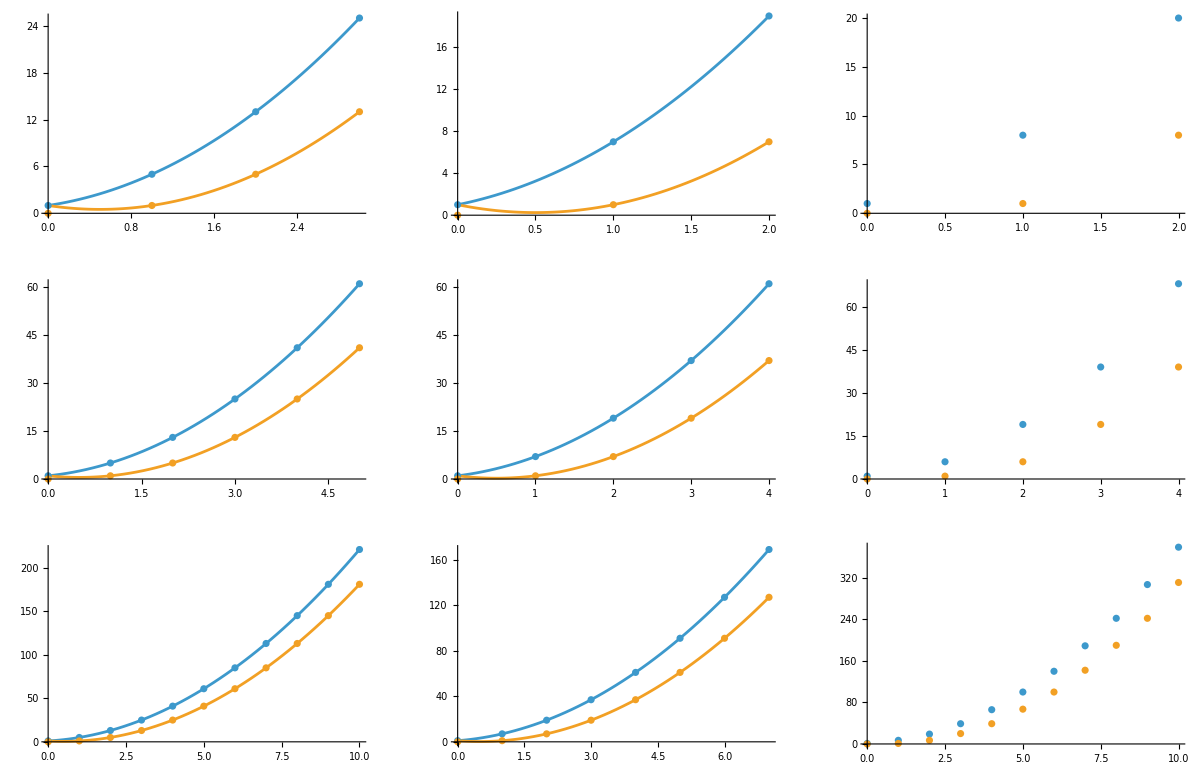

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size])},
    {radius = profileRadius[g]},
    {lattice = Switch[name, "SquareTilingGraph", 2 r^2 + 2 r + 1, "TriangularTilingGraph", 3 r^2 + 3 r + 1, _, Nothing]},
    Show[
      Plot[Evaluate[{lattice, lattice /. r -> r - 1}], {r, 0, radius}],
      ListPlot[twoMeasures[g, Table[InfraBall[InfraCenter[g], r], {r, 0, radius}]], DataRange -> {0, radius}],
      PlotRange -> All]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

On the tilings both profiles sit on their polynomials at every size: a tiling is a patch of its lattice, and a ball that stays one layer inside the patch counts as on the lattice.

On the mesh both profiles grow quadratically, with no closed form, and the Riemannian profile is again the counting profile one radius later.

[[ On the hexagonal tiling, does every vertex at distance r≥1 have a neighbour at distance r+1? Then its Riemannian ball count is 1+3/2 r(r-1), the counting polynomial 1+3/2 r(r+1) one radius earlier. ]]

## Shells

The shell is S_r(c)=={v:d(c,v)==r}, the outer layer of the ball. On the lattices it holds L(r)-L(r-1) vertices, 4r on the square lattice and 6r on the triangular one.

Its Riemannian measure is zero. Every vertex of S_r with r≥1 has a neighbour at distance r-1, which lies outside the shell, and the centre has a neighbour outside S_0. The whole shell is boundary.

In the continuum the geodesic sphere has area n ω_n r^(n-1)(1-Scal/(6n)r^2+O(r^4)) and volume zero. The two measures of a shell are its two readings: an area, counted, and a volume, which vanishes.

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size, "KeepCoordinates" -> True])},
    InfraSubstrateHighlight[g, interiorAndBoundary[g, InfraShell[InfraCenter[g], profileRadius[g]]]]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

The two profiles over r==0,…,R, against 4r and 6r.

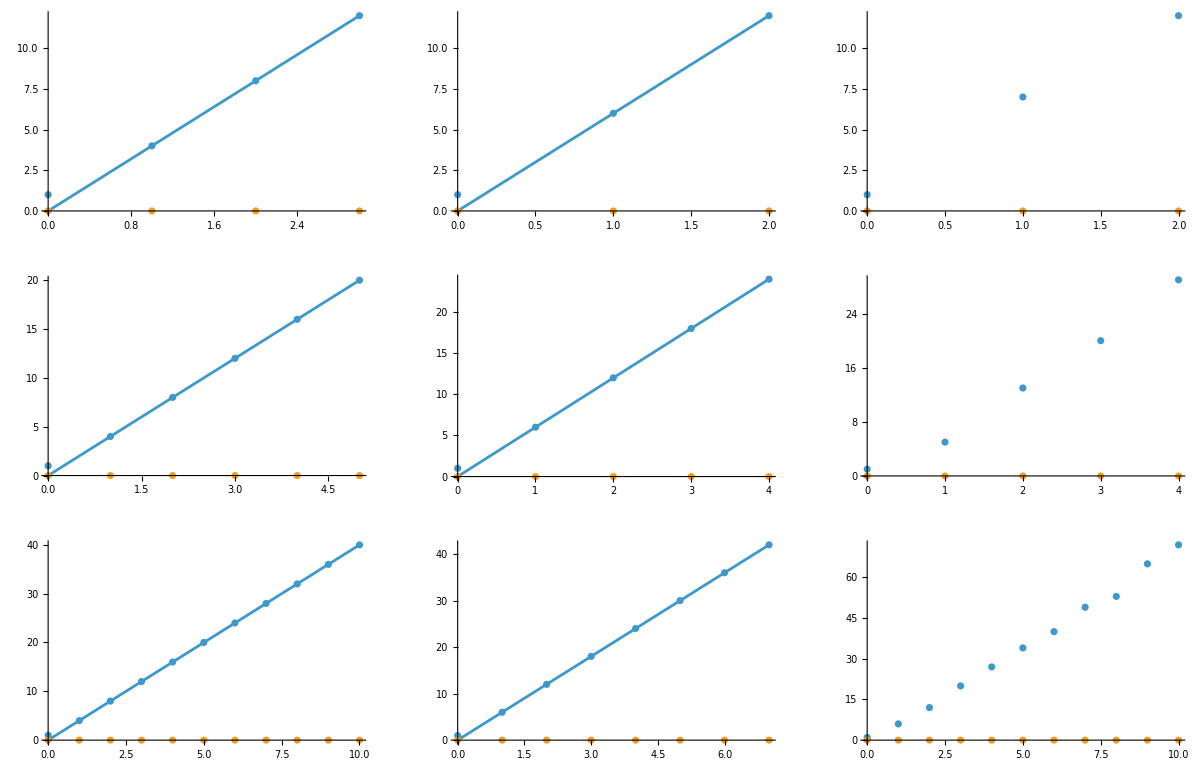

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size])},
    {radius = profileRadius[g]},
    {lattice = Switch[name, "SquareTilingGraph", 4 r, "TriangularTilingGraph", 6 r, _, Nothing]},
    Show[
      Plot[lattice, {r, 0, radius}],
      ListPlot[twoMeasures[g, Table[InfraShell[InfraCenter[g], r], {r, 0, radius}]], DataRange -> {0, radius}],
      PlotRange -> All]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

The counting profile is linear on the tilings and close to linear on the mesh; the Riemannian profile is zero everywhere.

## Tubes

The tube of thickness s about a set X is T_s(X)=={v:d(v,X)≤s}; the tube about one vertex is the ball.

Two cores join the centre c to the far end p. The fat tube is the tube about the interval I(c,p), the union of all geodesics from c to p: the head InfraTubepaclet:WolframInstitute/InfraGeometry/ref/InfraTubeWolframInstitute/InfraGeometry Package Symbol on the segment. The thin tube is the tube about one geodesic γ: the head on a representative of the segment.

The interior of a tube is one layer thinner: for s≥1, Int T_s(X)==T_(s-1)(X)∪{w:d(w,X)==s, no neighbour of w at distance s+1}. So the Riemannian measure of a tube is the counting measure of the tube one step thinner, together with the dead ends of its outer layer.

On the square lattice the interval is a box of sides a_1,a_2 with a_1+a_2==d(c,p), and the fat tube holds (a_1+1)(a_2+1)+2s(a_1+a_2+2)+2s(s-1) vertices. The thin tube about a staircase geodesic has no closed form.

In the continuum the thin tube is the counterpart of Gray's tube about a geodesic of length L, Vol T_s(γ)==ω_(n-1)s^(n-1)(L-s^2/(6(n+1))∫_γ (Scal+Ric(γ̇,γ̇))+O(s^4)), with the two end caps added; in Euclidean space the tube about a segment is the spherocylinder of volume ω_(n-1)s^(n-1)L+ω_n s^n. The fat tube has no such counterpart: its core is a box that grows with the offset of the two ends.

The tubes of thickness ⌈R/2⌉: the thin tube green, the rest of the fat tube blue, and the geodesic.

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size, "KeepCoordinates" -> True])},
    {c = InfraCenter[g], p = farEnd[g], thickness = Ceiling[profileRadius[g]/2]},
    {geodesic = FindInfraRepresentative[g, InfraSegment[c, p]]},
    {fat = FindInfraRepresentative[g, InfraTube[InfraSegment[c, p], thickness]], thin = FindInfraRepresentative[g, InfraTube[geodesic, thickness]]},
    InfraSubstrateHighlight[g, {Complement[fat, thin] -> $InfraCircleColor, thin -> $InfraBallColor, InfraWalk[geodesic] -> $InfraSegmentColor}]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

The profiles over s==0,…,R: the fat tube as joined points, the thin tube as points, the counting measure in the first colour and the Riemannian measure in the second. On the square tiling the curves are the box count and its value one step thinner.

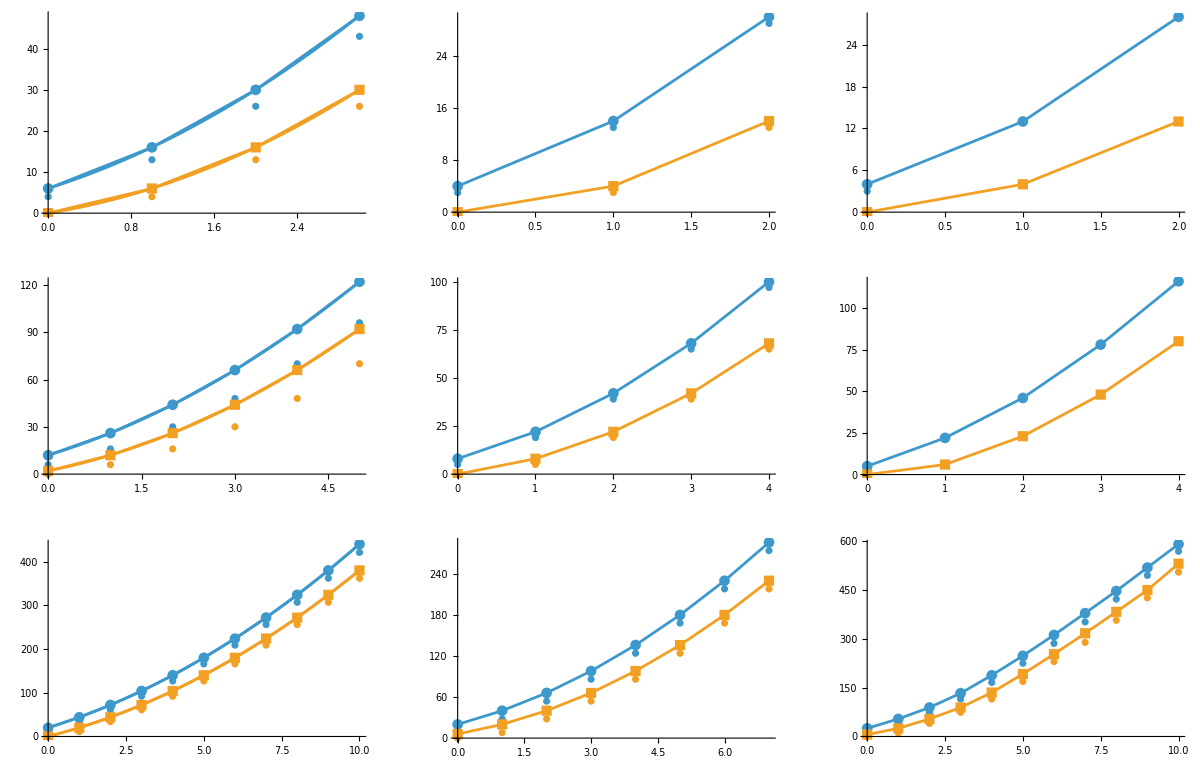

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size])},
    {c = InfraCenter[g], p = farEnd[g], radius = profileRadius[g]},
    {geodesic = FindInfraRepresentative[g, InfraSegment[c, p]]},
    {box = If[name == "SquareTilingGraph", InfraMeasurement[g, InfraSegment[c, p], "CountingMeasure"] + 2 s (radius + 2) + 2 s (s - 1), Nothing]},
    Show[
      Plot[Evaluate[{box, box /. s -> s - 1}], {s, 0, radius}],
      ListLinePlot[twoMeasures[g, Table[InfraTube[InfraSegment[c, p], s], {s, 0, radius}]], DataRange -> {0, radius}, PlotMarkers -> Automatic],
      ListPlot[twoMeasures[g, Table[InfraTube[geodesic, s], {s, 0, radius}]], DataRange -> {0, radius}],
      PlotRange -> All]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

The fat tube contains the thin one and outgrows it. On the square tiling the fat tube follows the box count, and its Riemannian measure is the count one step thinner.

## The ellipsoid

Two foci c,p at distance n bound the solid ellipsoid of slack k, E_k=={v:d(c,v)+d(v,p)≤n+k}, which FindInfraQuadricpaclet:WolframInstitute/InfraGeometry/ref/FindInfraQuadricWolframInstitute/InfraGeometry Package Symbol gives. At slack zero it is the interval I(c,p), the core of the fat tube.

On every graph T_s(I(c,p))⊆E_(2s). For x within s of a vertex y of the interval, two triangle inequalities through y give d(c,x)+d(x,p)≤d(c,y)+d(y,p)+2d(x,y)≤n+2s.

A median of three vertices lies on a geodesic between each two of them. If m is a median of c, p and x, then d(c,m)+d(m,p)==n, d(c,m)+d(m,x)==d(c,x) and d(p,m)+d(m,x)==d(p,x); adding the last two and subtracting the first gives 2d(m,x)==d(c,x)+d(x,p)-n. A median converts the slack of x into its distance from the interval, at the rate two.

A graph is modular when every three vertices have a median. On a modular graph a vertex of slack at most 2s has its median within s, so E_(2s)==T_s(I(c,p)): the ellipsoid of slack 2s is the fat tube of thickness s, under both measures.

In the Euclidean plane the two differ: the ellipse of slack k bulges to a half-width of order √nk in the middle, the tube keeps the half-width k/2. Under the ℓ^1 norm, |x+a|+|x-a|==2max(a,|x|), and the ellipse is the tube; the square lattice carries the ℓ^1 norm.

The ellipsoid of slack 2s and the fat tube of thickness s, for s==⌈R/2⌉: the tube in the ball colour, the vertices of the ellipsoid outside the tube red, and the interval.

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size, "KeepCoordinates" -> True])},
    {c = InfraCenter[g], p = farEnd[g], thickness = Ceiling[profileRadius[g]/2]},
    {ellipsoid = FindInfraQuadric[g, {c, p}, GraphDistance[g, c, p] + 2 thickness]},
    {tube = FindInfraRepresentative[g, InfraTube[InfraSegment[c, p], thickness]]},
    InfraSubstrateHighlight[g, {Complement[ellipsoid, tube] -> StandardRed, tube -> $InfraBallColor, InfraSegment[c, p]}]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

On the square tiling no vertex is red at any size: the ellipsoid is the tube. On the triangular tiling and on the mesh the ellipsoid reaches beyond the tube.

The profiles over s==0,…,R: the ellipsoid of slack 2s as joined points, the fat tube of thickness s as points, the counting measure in the first colour and the Riemannian measure in the second.

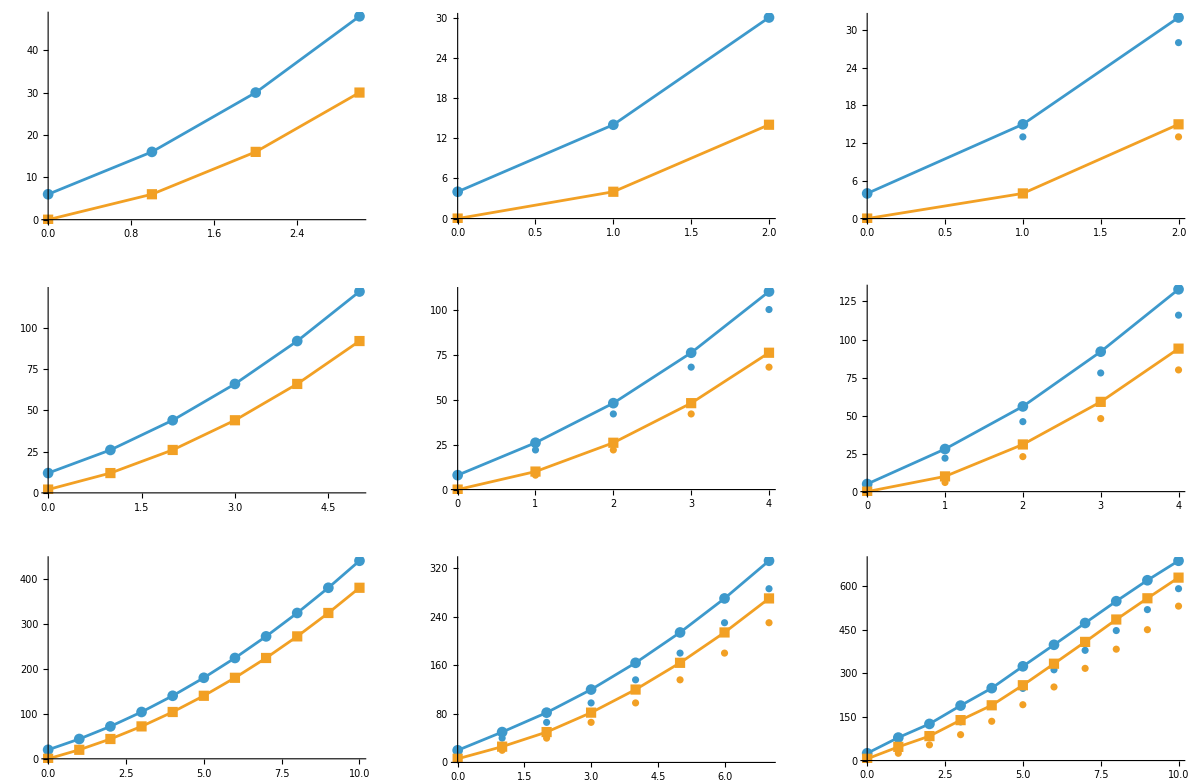

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size])},
    {c = InfraCenter[g], p = farEnd[g], radius = profileRadius[g]},
    Show[
      ListLinePlot[twoMeasures[g, Table[InfraTube[FindInfraQuadric[g, {c, p}, radius + 2 s], 0], {s, 0, radius}]], DataRange -> {0, radius}, PlotMarkers -> Automatic],
      ListPlot[twoMeasures[g, Table[InfraTube[InfraSegment[c, p], s], {s, 0, radius}]], DataRange -> {0, radius}],
      PlotRange -> All]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

On the square tiling the points sit on the joined points under both measures. On the triangular tiling and on the mesh the ellipsoid outgrows the tube, and the gap widens with s.

The modularity of the substrates themselves, checked rather than assumed: for every pair p,q and every vertex x, the triple has a median exactly when 2ⅆ(x,I(p,q))==d(p,x)+d(x,q)-d(p,q). Each vertex is inked by the number of pairs with which it has no median; the small substrates.

```mathematica
GraphicsRow @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, "Small", "KeepCoordinates" -> True])},
    {d = GraphDistanceMatrix[g], vertexTotal = VertexCount[g]},
    {lacking = Total @ Flatten[Table[
      With[{core = Pick[Range[vertexTotal], d[[i]] + d[[j]], d[[i, j]]]}, Unitize[2 (Min /@ d[[All, core]]) - (d[[i]] + d[[j]] - d[[i, j]])]],
      {i, vertexTotal}, {j, i + 1, vertexTotal}], 1]},
    InfraSubstrateHighlight[g, {Select[AssociationThread[VertexList[g], lacking], Positive]}]],
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

The small square tiling carries no ink: every triple has a median, the patch is modular, and the ellipsoid of slack 2s is the tube of thickness s for every pair of foci. The square lattice itself is a median graph, with the coordinatewise median.

On the triangular tiling and on the mesh every vertex lacks a median with some pair.

The smallest counterexample to the equality on the triangular tiling, with foci at distance two and thickness one: the corners a,b,x of a triangle of side two, with the three intervals between them.

```mathematica
With[
  {g = InfraSubstrate["TriangularTilingGraph", "Small", "KeepCoordinates" -> True]},
  {a = InfraCenter[g]},
  {beyond = focus |-> Complement[FindInfraQuadric[g, {a, focus}, 4], FindInfraRepresentative[g, InfraTube[InfraSegment[a, focus], 1]]]},
  {b = SelectFirst[FindInfraShell[g, a, 2], beyond[#] =!= {} &]},
  {x = First @ beyond[b]},
  InfraSubstrateHighlight[g, {InfraSegment[a, b], InfraSegment[b, x], InfraSegment[x, a], {a, b, x}}]]
```

-Graphics-

The three intervals are the three sides of the triangle, and no vertex lies on all three: a,b,x have no median. The corner x has slack two over the foci a,b, so it lies in the ellipsoid E_2, but its distance from the side I(a,b) is two, so it lies outside the tube T_1.

[[ On a non-modular substrate, is the gap between the ellipsoid of slack 2s and the tube of thickness s of the order s √ns, as for the Euclidean ellipse? ]]

## Cones

The cone of slope m about a geodesic γ==(γ_0,…,γ_n) from the apex c==γ_0 to p==γ_n is C_m(γ)=={v:d(v,γ_i)≤⌊mi⌋ for some i}: a ball of growing radius slid along γ.

For m≥1 the cone is the ball B_⌊mn⌋(p) about the far end: d(v,p)≤⌊mi⌋+n-i≤⌊mn⌋, on every graph.

For m<1 no closed lattice count is known. In the Euclidean plane the cone over a segment of length R is the convex hull of the apex and the disk of radius mR about the far end, of area R^2 m √(1-m^2)+m^2 R^2(π-arccosm). On a manifold the solid cone of radius r over a set Ω of unit directions has volume (σ(Ω))/n r^n-r^(n+2)/(6(n+2))∫_Ω Ric(u,u)ⅆu+O(r^(n+4)).

The cone of slope one half about one geodesic from the centre to the far end, by its two measures, with its axis.

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size, "KeepCoordinates" -> True])},
    {geodesic = FindInfraRepresentative[g, InfraSegment[InfraCenter[g], farEnd[g]]]},
    InfraSubstrateHighlight[g, Append[interiorAndBoundary[g, InfraCone[geodesic, 1/2]], InfraWalk[geodesic] -> $InfraSegmentColor]]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

The profiles over the slope m==0,1/8,…,3/2: the cone as points, the ball of radius ⌊mR⌋ about the far end as joined points, the counting measure in the first colour and the Riemannian measure in the second.

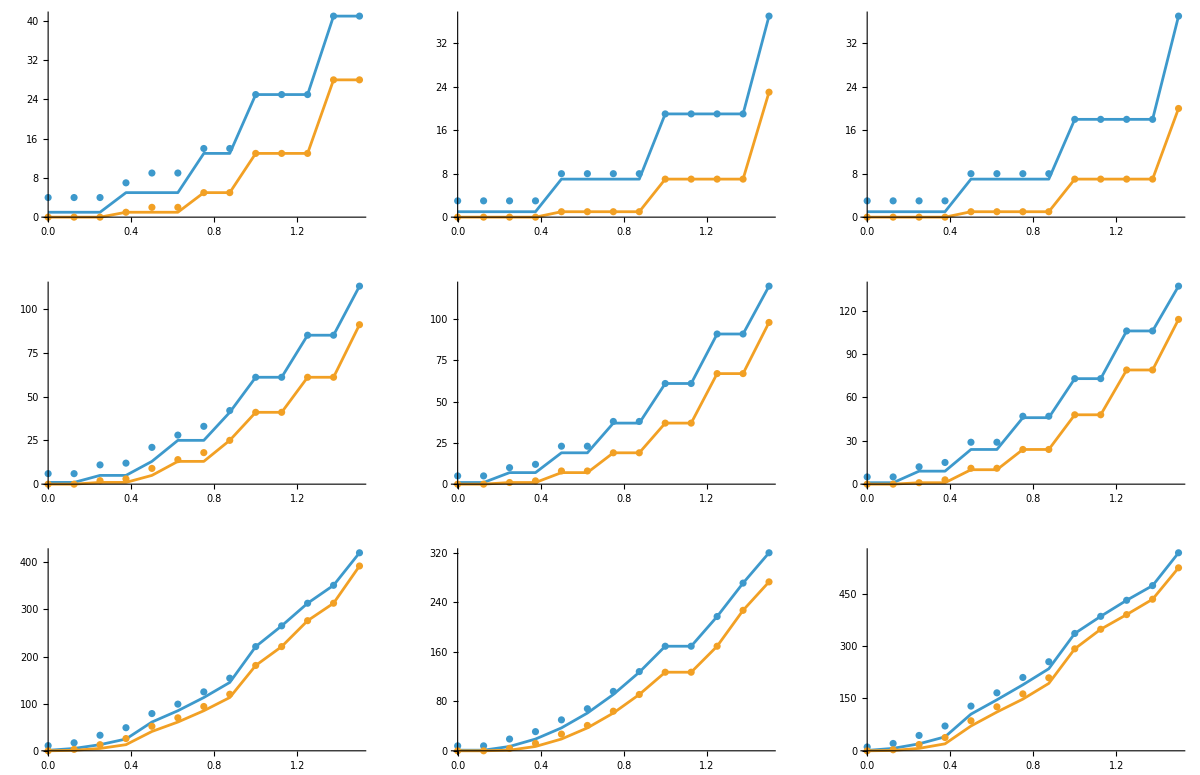

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size])},
    {p = farEnd[g], radius = profileRadius[g], slopes = Range[0, 3/2, 1/8]},
    {geodesic = FindInfraRepresentative[g, InfraSegment[InfraCenter[g], p]]},
    Show[
      ListLinePlot[twoMeasures[g, Table[InfraBall[p, Floor[m radius]], {m, slopes}]], DataRange -> {0, 3/2}],
      ListPlot[twoMeasures[g, Table[InfraCone[geodesic, m], {m, slopes}]], DataRange -> {0, 3/2}],
      PlotRange -> All]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

From slope one on, the cone is the far ball under both measures, on every substrate. Below slope one the cone contains the far ball and is larger: at slope zero it is the geodesic itself.

[[ For a rational slope 0<m<1, is the counting measure of the cone about a geodesic of length R in the square lattice a quasi-polynomial in R, and does it depend on the geodesic chosen in the interval? ]]

## Spheres

A set Σ in the band S_(r,s)(c)=={v:r≤d(c,v)≤s} separates if every path from c to a vertex beyond distance s meets Σ. A sphere instance of the band is a separating set that induces a connected subgraph and has no proper subset with both properties: a minimal wall around c. The head InfraSpherepaclet:WolframInstitute/InfraGeometry/ref/InfraSphereWolframInstitute/InfraGeometry Package Symbol is the family of instances; one instance, found greedily, is its representative.

In the band S_(r,r+1) the Riemannian measure of an instance is zero whenever every vertex at distance r+1 has a neighbour at distance r+2: every vertex of the band then has a neighbour outside it.

In the continuum an instance stands for the geodesic sphere, of area n ω_n r^(n-1)(1-Scal/(6n)r^2+O(r^4)). An instance is not a shell: no two vertices at one distance from c are adjacent on the square tiling, so a wall there zigzags between two shells.

One instance in the band between the radii ⌈R/2⌉ and ⌈R/2⌉+1, orange, drawn over the band, green.

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size, "KeepCoordinates" -> True])},
    {c = InfraCenter[g], inner = Ceiling[profileRadius[g]/2]},
    {wall = (SeedRandom[1]; FindInfraRepresentative[g, InfraSphere[c, {inner, inner + 1}]])},
    InfraSubstrateHighlight[g, {InfraShell[c, {inner, inner + 1}] -> $InfraShellColor, wall -> $InfraSegmentColor}]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

The profiles of one instance in each band S_(r,r+1) over r==1,…,min(R,6) as points, the counting measure in the first colour and the Riemannian measure in the second, with the counting measures of the two shells S_r and S_(r+1) as joined points.

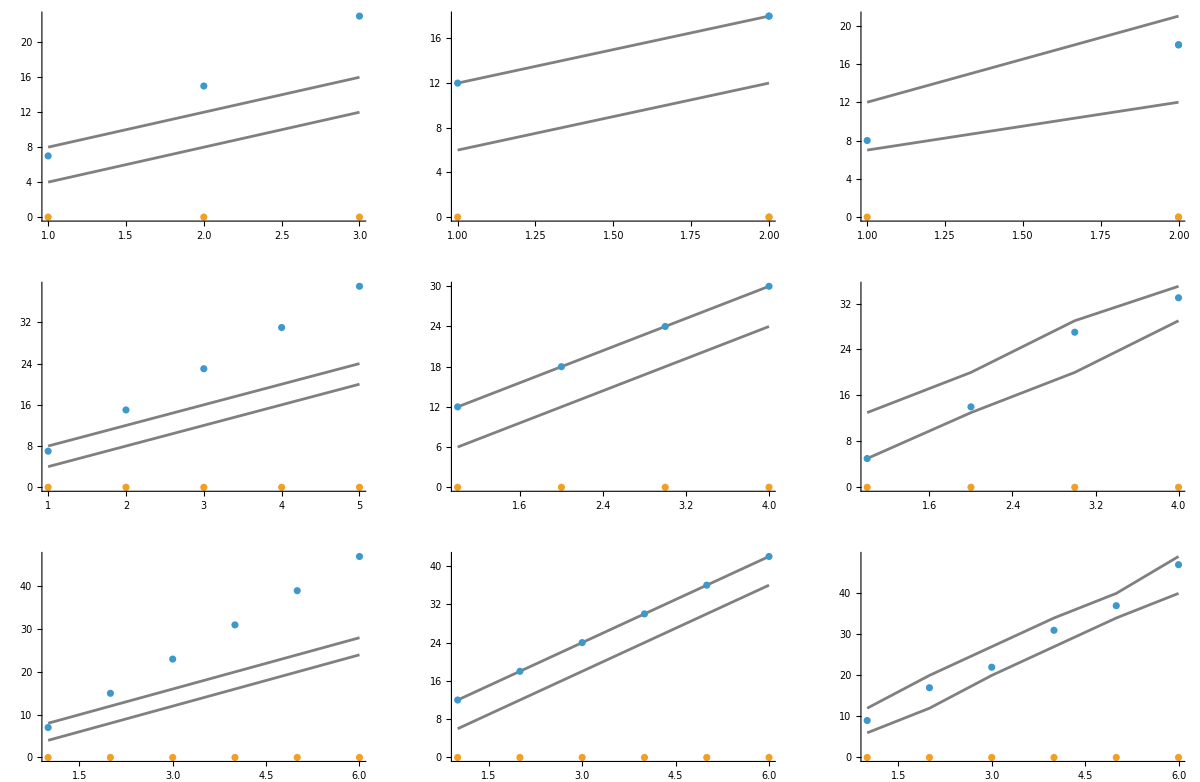

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size])},
    {c = InfraCenter[g], bandRadii = Range[1, Min[profileRadius[g], 6]]},
    {walls = Table[InfraTube[(SeedRandom[1]; FindInfraRepresentative[g, InfraSphere[c, {r, r + 1}]]), 0], {r, bandRadii}]},
    {shells = InfraMeasurement[g, Table[InfraShell[c, r], {r, First[bandRadii], Last[bandRadii] + 1}], "CountingMeasure"]},
    Show[
      ListLinePlot[{Transpose[{bandRadii, Most[shells]}], Transpose[{bandRadii, Rest[shells]}]}, PlotStyle -> Gray],
      ListPlot[Transpose[{bandRadii, #}] & /@ twoMeasures[g, walls]],
      PlotRange -> All]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

An instance grows linearly in r, like the shells of its band, and its Riemannian measure stays zero.

The instance found depends on the search. On the triangular tiling either shell of the band is an instance by itself, and the one found is the outer shell. On the square tiling a wall needs vertices of both shells and is larger than either.

[[ Is the size of the least sphere instance in the band S_(r,r+1) of a lattice a polynomial in r? ]]

## The measure

The two measures differ by a layer, and that layer holds a share of order 1/r of a ball. Which of them is the volume? The argument runs through a graph that approximates a manifold.

The approximating graph. Let M be a closed Riemannian manifold with normalized volume μ, and V⊂M a sample of N points whose mesh h==sup_(x∈M) min_(v∈V) d(x,v) is small. The Rips graph G_ϵ joins two points at distance less than ϵ; H_ϵ is its hop distance and ν_V==1/N∑_(v∈V) δ_v its normalized counting measure.

Topology. For every small scale ϵ and every sample dense enough for it, the clique complex of G_ϵ has the homotopy type of M (Latschev); quantitatively, 14h<ϵ<7/8 Δ suffices, with Δ a bound from the convexity radius and the sectional curvature (Majhi). The complex carries the topology, not the graph.

Distance. If 2h<ϵ, then d≤ϵ H_ϵ≤ϵ/(ϵ-2h)ⅆ+ϵ: a geodesic of length d cut into pieces of length below ϵ-2h, each division point moved to a sample point within h, is a path of the graph. As ϵ→0 and h/ϵ→0 the scaled hop distance converges uniformly to d, and shortest paths of the graph converge, along subsequences, to minimizing geodesics.

Volume. Coverage alone does not make ν_V approximate μ: equally spaced points on a circle, with as many again crowded on a short arc, have a small mesh and put half the mass on the arc. It does when the mesh tends to zero and the nearest-vertex cells C_v⊆B_h(v) have nearly equal volumes, and almost surely when the points are drawn independently from μ. Each vertex represents its cell, the centre of a ball included.

Balls. Let ϵ→0, h/ϵ→0 and ν_V→μ weakly, and let the hop radius r grow with ϵr→R. Both the closed graph ball B_r=={H_ϵ≤r} and the open one B_(r-1)=={H_ϵ<r} have normalized counts converging to μ(B_R(p)), since they lie between the geodesic balls of radii R-a and R+a with a→0, and the geodesic sphere has volume zero. Removing the outer graph layer is consistent, and it is not required.

The Riemannian measure counts the interior of B_r, and B_(r-1)⊆Int B_r⊆B_r, since a vertex at hop distance at most r-1 has all its neighbours within r. So the Riemannian measure converges to the same volume. The counting measure represents the ball of radius r read as a closed ball, the Riemannian measure represents it read as an open ball, and the argument singles out neither.

A Rips graph of points sprinkled in the unit square at the scale ϵ==N^(-1/3), for a growing number N of points, and the ball about the point nearest the middle at the hop radius closest to a quarter. Each point is drawn with its nearest-point cell: the cells of the interior green, of the boundary blue. The red circle has the radius r times the mean length of one hop from the centre.

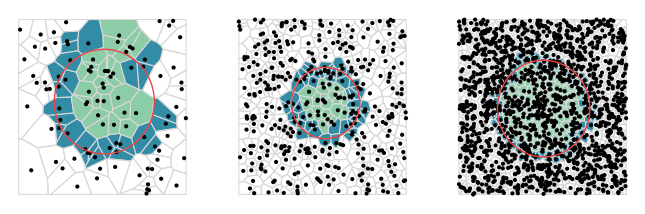

```mathematica
GraphicsRow @ Table[
  With[
    {points = (SeedRandom[2]; RandomPoint[Rectangle[], count])},
    {rips = NearestNeighborGraph[points, {All, count^(-1/3)}]},
    {c = First @ Nearest[points, {1/2, 1/2}]},
    {hop = Mean @ Map[pt |-> EuclideanDistance[pt, c]/GraphDistance[rips, c, pt], DeleteCases[points, c]]},
    {radius = Round[1/(4 hop)]},
    {ball = FindInfraRepresentative[rips, InfraBall[c, radius]]},
    {inner = InfraInterior[rips, ball]},
    Graphics[{
      Map[cell |-> With[{owner = First @ Nearest[points, RegionCentroid[cell]]},
        {EdgeForm[LightGray], Which[MemberQ[inner, owner], $InfraBallColor, MemberQ[ball, owner], $InfraCircleColor, True, FaceForm[]], cell}],
        MeshPrimitives[VoronoiMesh[points, {{0, 1}, {0, 1}}], 2]],
      Point[points], StandardRed, Circle[c, hop radius]}]],
  {count, {100, 400, 1600}}]
```

The cells of the closed ball overshoot the circle by about one layer of cells, the cells of the interior fall short of it by about as much. Both layers thin out as the sample refines, and both unions of cells approach the disk.

Exact evidence. On the cycle of N vertices, spacing a==1/N and R==ar, the ball of radius R has volume 2R, the closed graph ball has mass 2R+a and the open one 2R-a. The two one-layer conventions err by one vertex mass with opposite signs; half weight at the two end vertices gives 2R exactly.

The two measures of the ball of radius R==1/10 on cycles of growing length, divided by N, beside the volume 2R.

```mathematica
Grid[Prepend[
  Table[
    With[{g = CycleGraph[count]}, {ball = InfraBall[1, count/10]},
      {count, N[InfraMeasurement[g, ball, "RiemannianMeasure"]/count], N[1/5], N[InfraMeasurement[g, ball, "CountingMeasure"]/count]}],
    {count, {100, 200, 400}}],
  {"N", "Riemannian", "volume", "counting"}], Frame -> All]
```

N | Riemannian | volume | counting
100 | 0.19 | 0.2 | 0.21
200 | 0.195 | 0.2 | 0.205
400 | 0.1975 | 0.2 | 0.2025

On the square lattice with spacing a, vertex area a^2 and R==ar, the closed and the open count give 2 R^2+2aR+a^2 and 2 R^2-2aR+a^2, against the area 2 R^2 of the ℓ^1 ball: relative errors ±a/R+a^2/(2 R^2). Deleting the outer layer reverses the linear correction and keeps the constant term.

The two measures of the balls about the centre over r==0,…,R as points, against the continuum volume counted in vertex cells. Here the columns are the square tiling, the mesh of the unit square and a mesh of the unit sphere. The continuum volume is, in turn, the area 2 r^2 of the ℓ^1 ball, the area of the disk of radius ar times the number of vertices, and the area of the cap of angular radius ar times the number of vertices per unit area. The hop length a is the mean distance of a vertex from the centre per hop, in the metric of the continuum: on the square tiling the ℓ^1 metric of the lattice, which in the stored coordinates, turned by an eighth of a turn, is the chessboard metric; on the square the Euclidean metric; on the sphere the angle.

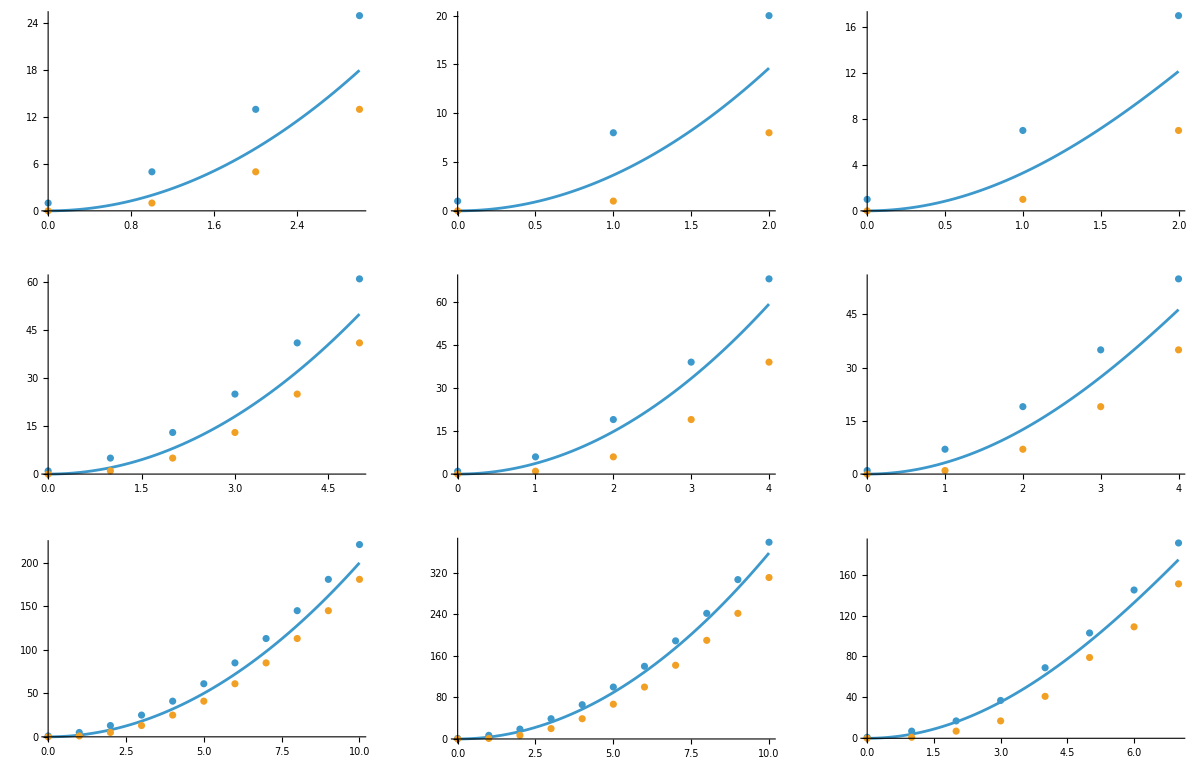

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[First[spec], size, "KeepCoordinates" -> True])},
    {c = InfraCenter[g], radius = profileRadius[g], where = AssociationThread[VertexList[g], GraphEmbedding[g]]},
    {hop = Mean @ Map[pt |-> spec[[2]][where[pt], where[c]]/GraphDistance[g, c, pt], DeleteCases[VertexList[g], c]]},
    Show[
      Plot[spec[[3]][hop r, VertexCount[g]], {r, 0, radius}],
      ListPlot[twoMeasures[g, Table[InfraBall[c, r], {r, 0, radius}]], DataRange -> {0, radius}],
      PlotRange -> All]],
  {size, {"Small", "Medium", "Large"}},
  {spec, {
    {"SquareTilingGraph", ChessboardDistance, {rho, total} |-> 2 rho^2},
    {"SquareMeshGraph", EuclideanDistance, {rho, total} |-> total Pi rho^2},
    {"SphereMeshGraph", VectorAngle, {rho, total} |-> total (1 - Cos[rho])/2}}}]
```

On every substrate the continuum volume runs between the two measures: the counting measure above, the Riemannian measure below, one layer of vertices apart.

The centre. The ball of radius zero has counting measure one and Riemannian measure zero, and neither is wrong. The centre represents its cell; a ball of physical radius below the spacing contains only the centre, and its volume exponent is zero. A dimension appears only over a range of resolved scales, h≪ϵ≪R→0, and there closed balls and balls rounded by one hop have the same asymptotics.

[[ Which weighting of the boundary, such as half weight on it as on the cycle, makes the error second order on a mesh? ]]

## Dimension

On a space of dimension d the ball volume grows like r^d. The log-difference quotient Δ(r)==(logV(r+1)-logV(r))/(log(r+1)-logr) is the slope of logV against logr between two radii, and LogDifferenceQuotientspaclet:WolframInstitute/InfraGeometry/ref/LogDifferenceQuotientsWolframInstitute/InfraGeometry Package Symbol computes it.

For a polynomial profile of degree d with leading coefficient c_d and next coefficient c_(d-1), Δ(r)==d-(c_(d-1)/c_d)/r+O(r^-2). For a lattice ball count c_(d-1)/c_d==d/2, so the counting profile L(r) gives d-d/(2r), from below, and the Riemannian profile L(r-1) gives d+d/(2r), from above, at the same rate.

The technical introduction of the Wolfram Physics Project, section 4.5, defines V_r as the number of vertices within distance r and Δ(r) as above. Its code applies the log-differences to the list V_0,V_1,V_2,… that starts at radius zero, so the value it plots at radius r is computed from V_(r-1). On a lattice V_(r-1) is the count of the interior of B_r: the introduction reads the Riemannian measure.

The introduction's code, beside the quotients of the paclet's two profiles, on the grid graph of the introduction.

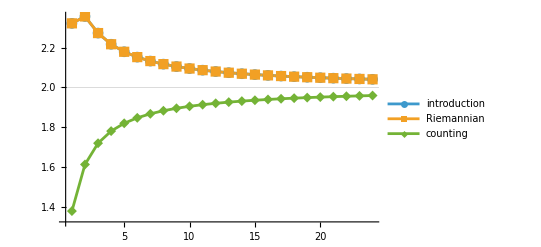

```mathematica
With[
  {g = GridGraph[{51, 51}]},
  {c = First @ GraphCenter[g]},
  {ballVolumes = InfraMeasurement[g, Table[InfraBall[c, r], {r, 0, 25}], "CountingMeasure"]},
  ListLinePlot[{
      Take[ResourceFunction["LogDifferences"][N @ First @ Values @ ResourceFunction["GraphNeighborhoodVolumes"][g, {c}]], 24],
      LogDifferenceQuotients[N @ InfraMeasurement[g, Table[InfraBall[c, r], {r, 1, 25}], "RiemannianMeasure"]],
      LogDifferenceQuotients[N @ Rest[ballVolumes]]},
    PlotLegends -> {"introduction", "Riemannian", "counting"}, PlotMarkers -> Automatic, GridLines -> {None, {2}}, PlotRange -> All]]
```

The introduction's curve is the Riemannian curve, point for point. The counting curve, each volume at its own radius, approaches two from below: the two readings of one profile differ most at small radius, where the dimension is read.

The two curves on the substrates: the counting curve Δ of r↦|B_r| in the first colour, the Riemannian curve Δ of r↦|Int B_r| in the second, over the radii below the eccentricity of the centre. The curves are 2-1/r and 2+1/r, the two rates of the planar lattices, and the line is the dimension two.

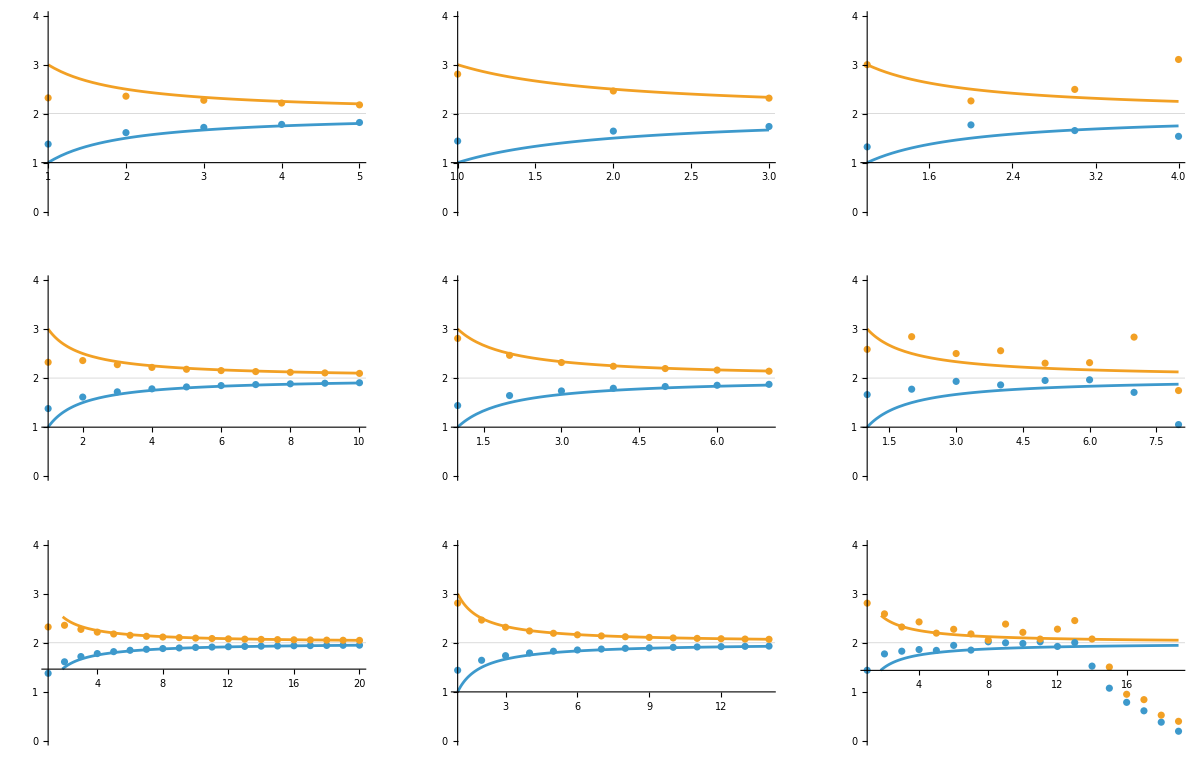

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size])},
    {c = InfraCenter[g]},
    {top = VertexEccentricity[g, c]},
    Show[
      Plot[{2 - 1/r, 2 + 1/r}, {r, 1, top - 2}],
      ListPlot[LogDifferenceQuotients /@ N[twoMeasures[g, Table[InfraBall[c, r], {r, 1, top - 1}]]]],
      GridLines -> {None, {2}}, PlotRange -> {0, 4}]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

On every substrate the counting curve rises towards two from below and the Riemannian curve falls towards it from above, until the balls meet the rim of the substrate.

The two curves part most at small radius, where a finite substrate is read. Their mean is d+O(r^-2) on the lattices.

### The row of section 4.5

The figures of the introduction's section, measured with the heads of this paclet: the balls through InfraBallpaclet:WolframInstitute/InfraGeometry/ref/InfraBallWolframInstitute/InfraGeometry Package Symbol and InfraMeasurementpaclet:WolframInstitute/InfraGeometry/ref/InfraMeasurementWolframInstitute/InfraGeometry Package Symbol, the quotients through LogDifferenceQuotientspaclet:WolframInstitute/InfraGeometry/ref/LogDifferenceQuotientsWolframInstitute/InfraGeometry Package Symbol. Each quotient plot shows the introduction's reading, the profile from radius zero, as joined points, the counting curve at its own radius as points, and the reference dimension as a line.

The grids of dimension one, two and three, and their balls of radius zero to five about the centre.

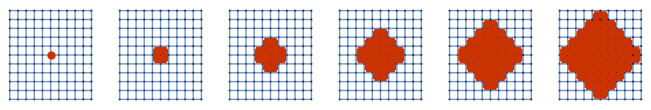
-Graphics-
-Graphics-
-Graphics-

```mathematica
Column @ Table[
  With[
    {g = GridGraph[sides]},
    {c = First @ GraphCenter[g]},
    GraphicsRow @ Table[InfraSubstrateHighlight[g, {InfraBall[c, r]}], {r, 0, 5}]],
  {sides, {{11}, {11, 11}, {7, 7, 7}}}]
```

The ball volumes of the finite grids against the infinite grid, L_d(r)==∑_k 2^k Binomial[d, k]Binomial[r, k], and against the leading term 2^d/(d!)r^d.

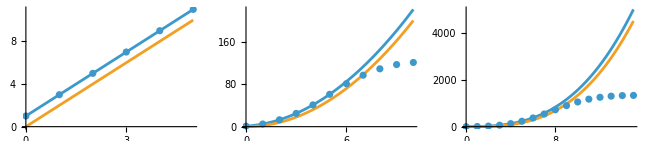

```mathematica
GraphicsRow @ Table[
  With[
    {g = GridGraph[ConstantArray[11, dim]]},
    {c = First @ GraphCenter[g]},
    {top = VertexEccentricity[g, c]},
    Show[
      Plot[{Sum[2^k Binomial[dim, k] Binomial[r, k], {k, 0, dim}], 2^dim r^dim/dim!}, {r, 0, top}],
      ListPlot[InfraMeasurement[g, Table[InfraBall[c, r], {r, 0, top}], "CountingMeasure"], DataRange -> {0, top}],
      PlotRange -> All]],
  {dim, 3}]
```

The quotients at the centres of grids of dimension one, two and three.

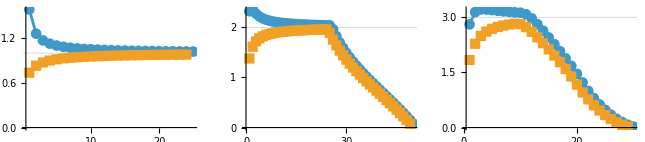

```mathematica
GraphicsRow @ Table[
  With[
    {g = GridGraph[ConstantArray[First[spec], Last[spec]]]},
    {c = First @ GraphCenter[g]},
    {ballVolumes = N @ Table[InfraMeasurement[g, InfraBall[c, r], "CountingMeasure"], {r, 0, VertexEccentricity[g, c]}]},
    ListLinePlot[{LogDifferenceQuotients[ballVolumes], LogDifferenceQuotients[Rest[ballVolumes]]}, PlotMarkers -> Automatic, Joined -> {True, False}, GridLines -> {None, {Last[spec]}}, PlotRange -> All]],
  {spec, {{51, 1}, {51, 2}, {21, 3}}}]
```

The triangulated rectangle of the introduction, and its balls of radius one to six about the centre.

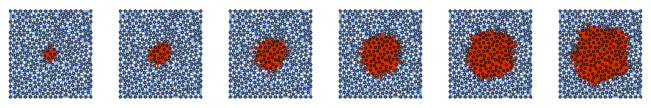

```mathematica
With[
  {g = MeshConnectivityGraph[DiscretizeRegion[Rectangle[], MaxCellMeasure -> 0.002]]},
  {c = First @ GraphCenter[g]},
  GraphicsRow @ Table[InfraSubstrateHighlight[g, {InfraBall[c, r]}], {r, 6}]]
```

Its quotients, the profiles averaged over the centres and their neighbours.

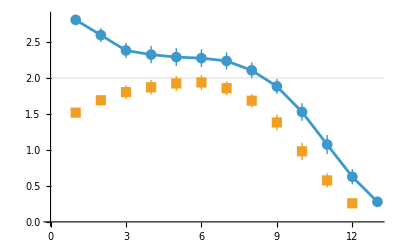

```mathematica
With[
  {g = MeshConnectivityGraph[DiscretizeRegion[Rectangle[], MaxCellMeasure -> 0.002]]},
  {seeds = VertexList @ NeighborhoodGraph[g, GraphCenter[g], 1]},
  {top = Min[VertexEccentricity[g, #] & /@ seeds]},
  {ballVolumes = MeanAround /@ Transpose @ Table[InfraMeasurement[g, Table[InfraBall[seed, r], {r, 0, top}], "CountingMeasure"], {seed, seeds}]},
  ListLinePlot[{LogDifferenceQuotients[ballVolumes], LogDifferenceQuotients[Rest[ballVolumes]]}, PlotMarkers -> Automatic, Joined -> {True, False}, GridLines -> {None, {2}}]]
```

The Sierpinski graphs of six and seven steps, against the Hausdorff dimension log3/log2. The introduction averages the profiles over all vertices, here over a random sample of them.

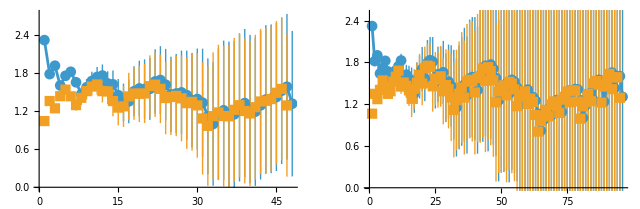

```mathematica
GraphicsRow @ Table[
  With[
    {g = IndexGraph[MeshConnectivityGraph[SierpinskiMesh[steps], 0]]},
    {top = GraphRadius[g], seeds = (SeedRandom[3]; RandomSample[VertexList[g], 64])},
    {ballVolumes = MeanAround /@ Transpose @ Table[InfraMeasurement[g, Table[InfraBall[seed, r], {r, 0, top}], "CountingMeasure"], {seed, seeds}]},
    ListLinePlot[{LogDifferenceQuotients[ballVolumes], LogDifferenceQuotients[Rest[ballVolumes]]}, PlotMarkers -> Automatic, Joined -> {True, False}, GridLines -> {None, {Log[2, 3]}}]],
  {steps, {6, 7}}]
```

The binary tree of eleven levels, the profiles averaged over a random sample of vertices.

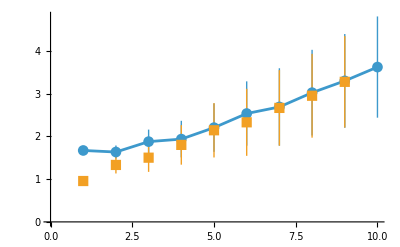

```mathematica
With[
  {g = KaryTree[2047]},
  {top = GraphRadius[g], seeds = (SeedRandom[3]; RandomSample[VertexList[g], 64])},
  {ballVolumes = MeanAround /@ Transpose @ Table[InfraMeasurement[g, Table[InfraBall[seed, r], {r, 0, top}], "CountingMeasure"], {seed, seeds}]},
  ListLinePlot[{LogDifferenceQuotients[ballVolumes], LogDifferenceQuotients[Rest[ballVolumes]]}, PlotMarkers -> Automatic, Joined -> {True, False}]]
```

Two Wolfram models, in the introduction's reading only. The first at the centre of its states after 500, 1000, …, 2500 steps; the second averaged over a random sample of vertices of the same states. Both against the dimension two.

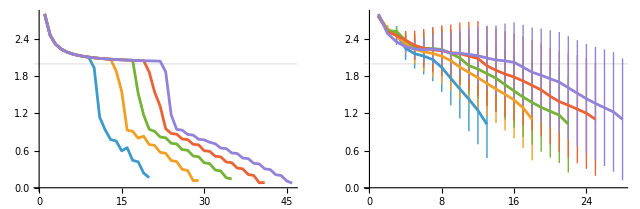

```mathematica
GraphicsRow @ Table[
  Show[
    ListLinePlot[
      Table[
        With[
          {g = UndirectedGraph @ ResourceFunction["HypergraphToGraph"][Quiet @ ResourceFunction["WolframModel"][First[spec], {{0, 0, 0}, {0, 0, 0}}, steps, "FinalState"]]},
          {top = GraphRadius[g], seeds = If[Last[spec], (SeedRandom[3]; RandomSample[VertexList[g], 32]), {First @ GraphCenter[g]}]},
          LogDifferenceQuotients[MeanAround /@ Transpose @ Table[InfraMeasurement[g, Table[InfraBall[seed, r], {r, 0, top}], "CountingMeasure"], {seed, seeds}]]],
        {steps, 500, 2500, 500}]],
    GridLines -> {None, {2}}],
  {spec, {{{{1, 2, 2}, {3, 1, 4}} -> {{2, 5, 2}, {2, 3, 5}, {4, 5, 5}}, False}, {{{1, 1, 2}, {1, 3, 4}} -> {{4, 4, 5}, {5, 4, 2}, {3, 2, 5}}, True}}}]
```

On the grids and the mesh the introduction's reading approaches the dimension from above, and the counting curve at its own radius from below; the two differ most at the small radii, which are all a finite graph has. On the Sierpinski graphs both readings oscillate about the Hausdorff dimension, the introduction's above the other at small radii.

The binary tree has no finite dimension under either reading: its quotients grow with the radius, as its ball volume grows exponentially. The two models settle near two as they grow.

Related Guides

RiemannianInfrageometrypaclet:WolframInstitute/InfraGeometry/guide/RiemannianInfrageometry ▪ EuclideanInfrageometrypaclet:WolframInstitute/InfraGeometry/guide/EuclideanInfrageometry

Related Tech Notes

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraGeometry

WolframInstitute`InfraGeometry`

WolframInstitute/InfraGeometry/tutorial/VolumeMeasurementTutorial

### Keywords

volume

ball

shell

tube

ellipsoid

quadric

cone

sphere

counting measure

Riemannian measure

Rips graph

median

modular graph

dimension

log-difference quotient

Wolfram Physics